```mathematica
Clear["Global`*"]
```

```mathematica
<<sneg`sneg`;
```

sneg 2.0.3 Copyright (C) 2002-2022 Rok Zitko

```mathematica
snegfermionoperators[c];
snegrealconstants[ntot,J2,χ];
```

```mathematica
PrettyOutputBraKetRule={ 
Null->"∘", 
1/2 ->StyleBox["↑",FontColor->Red],
-1/2->StyleBox["↓",FontColor->Blue]};
```

```mathematica
ntot=3;
b1=makebasis[Table[c[i],{i,1,ntot}]];
bz=Flatten@Apply[Outer,Prepend[Partition[b1,2],nc]];
(*bvc=ap[#,vacuum[]]&/@bz*)
bsp=Flatten@Apply[Outer,Prepend[Table[{1/2,-1/2},3],ket]]
n2state[nstate_]:=nstate.bsp
```

{|↑↑↑⟩,|↑↑↓⟩,|↑↓↑⟩,|↑↓↓⟩,|↓↑↑⟩,|↓↑↓⟩,|↓↓↑⟩,|↓↓↓⟩}

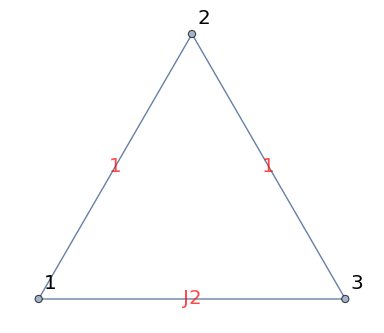

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->{1,1,J2},VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeLabelStyle->Directive[Red,20],VertexLabelStyle->Directive[Black,20]]
```

```mathematica
H=spinspin[c[1],c[2]]+spinspin[c[2],c[3]]+J2 spinspin[c[3],c[1]];
```

```mathematica
H1
```

1/4 (-(c_(1↓)^†·c_(2↓)^†·c_(1↓)^·c_(2↓)^)+c_(1↓)^†·c_(2⇑)^†·c_(1↓)^·c_(2⇑)^-2 c_(1↓)^†·c_(2⇑)^†·c_(1⇑)^·c_(2↓)^-2 c_(1⇑)^†·c_(2↓)^†·c_(1↓)^·c_(2⇑)^+c_(1⇑)^†·c_(2↓)^†·c_(1⇑)^·c_(2↓)^-c_(1⇑)^†·c_(2⇑)^†·c_(1⇑)^·c_(2⇑)^)+1/4 J2 (-(c_(1↓)^†·c_(3↓)^†·c_(1↓)^·c_(3↓)^)+c_(1↓)^†·c_(3⇑)^†·c_(1↓)^·c_(3⇑)^-2 c_(1↓)^†·c_(3⇑)^†·c_(1⇑)^·c_(3↓)^-2 c_(1⇑)^†·c_(3↓)^†·c_(1↓)^·c_(3⇑)^+c_(1⇑)^†·c_(3↓)^†·c_(1⇑)^·c_(3↓)^-c_(1⇑)^†·c_(3⇑)^†·c_(1⇑)^·c_(3⇑)^)+1/4 (-(c_(2↓)^†·c_(3↓)^†·c_(2↓)^·c_(3↓)^)+c_(2↓)^†·c_(3⇑)^†·c_(2↓)^·c_(3⇑)^-2 c_(2↓)^†·c_(3⇑)^†·c_(2⇑)^·c_(3↓)^-2 c_(2⇑)^†·c_(3↓)^†·c_(2↓)^·c_(3⇑)^+c_(2⇑)^†·c_(3↓)^†·c_(2⇑)^·c_(3↓)^-c_(2⇑)^†·c_(3⇑)^†·c_(2⇑)^·c_(3⇑)^)

```mathematica
Hχ=χ 
H=H1+Hχ;
```

χ

```mathematica
spinxyz[c[1]]
```

{1/2 (c_(1↓)^†·c_(1⇑)^+c_(1⇑)^†·c_(1↓)^),1/2 (ⅈ c_(1↓)^†·c_(1⇑)^-ⅈ c_(1⇑)^†·c_(1↓)^),1/2 (-(c_(1↓)^†·c_(1↓)^)+c_(1⇑)^†·c_(1⇑)^)}

```mathematica
m=matrixrepresentationop[H,bz];
```

```mathematica
{spectrum,eigvecs}=Eigensystem[m]
```

{{1/4 (-4+J2),1/4 (-4+J2),-(3 J2)/4,-(3 J2)/4,(2+J2)/4,(2+J2)/4,(2+J2)/4,(2+J2)/4},{{0,0,0,1,0,-2,1,0},{0,1,-2,0,1,0,0,0},{0,0,0,-1,0,0,1,0},{0,-1,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,1,1,0},{0,1,1,0,1,0,0,0},{1,0,0,0,0,0,0,0}}}

```mathematica
state[i_]:=n2state@eigvecs[[i]]
```

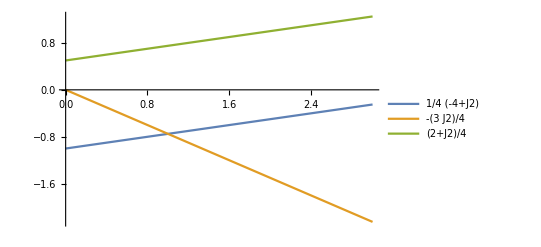

```mathematica
Plot[Evaluate@DeleteDuplicates@spectrum,{J2,0,3},PlotLegends->"Expressions"]
```

```mathematica
state/@{1,3,5}
```

{|↓↓↑⟩-2|↓↑↓⟩+|↑↓↓⟩,|↓↓↑⟩-|↑↓↓⟩,|↓↓↓⟩}